```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

```mathematica
(* nb code in Renormalisatios might be better than n Classifying*)
```

## Txb0501VanItersonMain

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};

jLaTeXBodyStyle = Directive[FontFamily->  jStyle["LaTeXBodyFamily"],FontSize->12];  jLaTeXNumberStyle = Directive[FontFamily->  jStyle["LaTeXDefaultFamily"],FontSize->12];  (* garamond has old-style numbers *) 
jLaTeXMathsStyle = Directive[FontFamily->  jStyle["LaTeXDefaultFamily"],FontSlant->Italic,FontSize->12];
jGraphLabelStyle = Directive[FontFamily->   jStyle["FontFamily"]]; (* ie gill *)




viSwatch = <| "TouchingCircle"->  jParastichyColour[1]
,"OpposedTouchingCircle"-> jParastichyColour[1]
,"NonOpposedTouchingCircle"->jStyle["CylinderColour"]
,"FibonacciBranch"-> jParastichyColour[1]
,"NonFibonacciBranch"-> jStyle["CylinderColour"]
,"NonTouchingCircle"-> LightGray |>;

triplePointLabelColour = jStyle["CylinderColour"];
branchLabelColour =  Lighter[jParastichyColour[1]];
setGill = Directive[FontFamily->jStyle["FontFamily"],FontSize->14];

ffs = Directive[FaceForm[None],EdgeForm[Gray]];
```

```mathematica
triplePointLabel[mn_] := Module[{at,m,n,str1,gr},
{m,n}= mn;
at = vanItersonRegionPoints[mn]["LeftTriplePoint"];
str1 = Style[StringTemplate["``=``=``"][m,n,m+n],Background->triplePointLabelColour,FontFamily->jStyle["DisplayFontFamily"]];
gr  = Inset[TextGrid[{{str1}},Frame->None,Alignment->Center],at];
gr
];


touchingCircleLabel[mn_] := Module[{at,m,n,str1,gr},
{m,n}= mn;
at =vanItersonRegionPoints[mn]["TouchingCircle"];
str1 = Style[StringTemplate["``=``"][m,n],Background->branchLabelColour,FontFamily->jStyle["DisplayFontFamily"]];
gr  = Inset[TextGrid[{{str1}},Frame->None,Alignment->Center],at];
gr
];

touchingCircleLabelNonPrimary[mn_] := Module[{at,m,n,str1,gr},
{m,n}= mn;
at =vanItersonRegionPoints[{n-m,n}]["UpperTouchingCircle"];
str1 = Style[StringTemplate["``=``"][Abs[m],n],Background->branchLabelColour,FontFamily->jStyle["DisplayFontFamily"]];
gr  = Inset[TextGrid[{{str1}},Frame->None,Alignment->Center],at];
gr
];
regionLabel[mnp_] := Style[panelLabel[mnp,vanItersonLabelPoint[mnp],0.25],Directive[Background->White,Frame->True]];

panelLabelBothSides [mn_,at_,scaling_:0.08] := Module[{obj,reflect},
reflect[{x_,y_}] := {1-x,y};
{panelLabel[mn,at,scaling],panelLabel[mn,reflect[at],scaling]}
];

panelLabel [{m_,n_},at_,scaling_:0.08] := Module[{textsize,obj},
textsize[{x_,y_}] := Scaled[scaling * Min[Sqrt[y],0.5]];
obj=Grid[
{{Style[StringTemplate["``,``"][m,n],FontFamily->jStyle["DisplayFontFamily"],FontSize->textsize[at]]}}
,Frame->None
];
Inset[obj,at]
];

rColours["01","Plus"] = ColorData[50,1];
rColours["01","Minus"] = ColorData[50,2];
rColours["10","Plus"] =  ColorData[50,7];
rColours["10","Plus",1] =  ColorData[50,7];
rColours["10","Plus",-1] =  ColorData[50,5];
rColours["10","Minus"] =  ColorData[50,4];
```

```mathematica
QwRed := Directive[Thin,viSwatch["TouchingCircle"]];



Ch4FullTreePlot[mnPairs_,labelPairs_,opts:OptionsPattern[]] := Module[{regionLabel,hmax,plotRange,boundaries},

regionLabel[mn_]   := {
panelLabelBothSides[mn,vanItersonLabelPoint[mn]],
panelLabelBothSides[Reverse[mn],vanItersonLabelPoint[Reverse[mn]]]
};
regionLabel[{0,1}] = panelLabelBothSides[{0,1},{0.2,1.05}];
regionLabel[{1,0}] = panelLabelBothSides[{1,0},{0.2,0.8}];

hmax = 1.2;
plotRange = PlotRange  /. List@opts;

boundaries = {
{Thin,LightGray,Map[vanItersonTouchingCircleNonPrimary,mnPairs]/. ∞-> plotRange⟦2,2⟧}
,
{Thin,viSwatch["TouchingCircle"],Map[vanItersonTouchingCirclePrimary,mnPairs]}
}; (* if plot in reverse order then see a bug for 1,2 *)

Graphics[
{  
{Thin,LightGray,Line[{{1,0},{1,hmax}}]}
,{boundaries,GeometricTransformation[boundaries,ReflectionTransform[{1,0},{1/2,0}]]}
,Map[regionLabel,labelPairs]
},
Evaluate[FilterRules[{opts}, Options[Graphics]]]
]
];


pairsTodo[hmin_,imax_] := Module[{n,ntodo,hm,res,makeP},
ntodo[m_,hm_] := Ceiling[Sqrt[m^2+ 1/hm]];
makeP[i_,hm_] := Select[Table[{i,j},{j,i+1,ntodo[i,hm]}],CoprimeQ[i,#[[2]]]&];
res= Select[ Table[makeP[i,hmin],{i,imax}],Length[#]>0&];
res=Flatten[res,1];
res
];

 addSubTree[mnpairs_] := DeleteDuplicates@Flatten[Map[ {#,{#⟦1⟧,#⟦1⟧+#⟦2⟧},{#⟦2⟧,#⟦1⟧+#⟦2⟧}}&,mnpairs],1];
```

```mathematica
Ch4VanItersonMain := Module[{mnPairs,labelPairs},
mnPairs  = Join [{ {0,1},{1,1}},pairsTodo[.005,50]];
labelPairs = Join[{{1,0}},Nest[addSubTree,{{0,1}},4],{{1,5},{4,5}}];
Ch4FullTreePlot[ mnPairs,labelPairs
,PlotRange->{{0,1},{0,1.2}}
,Axes->True
,ImageSize->jStyle["FullWidthImagePT"]
,PlotRangeClipping->True
,Ticks-> {{0,1/2,1},{0,1}}
,TicksStyle-> jGraphLabelStyle
,AxesLabel-> Map[Style[#,Italic,FontFamily->jStyle["FontFamily"]]&,{"d","h"}]
]
];
```

```mathematica
Txb0501VanItersonMain =Ch4VanItersonMain;
txbExport[Txb0501VanItersonMain]
```

-Graphics-

## Txb0502VanItersonZoom

```mathematica
mnAbove[{m_,n_}] := {Abs[n-m],Min[m,n]};


colourPolygonNew[mn_] := Module[{sig},
sig = If[euclideanDelta[mn]>0,"01","10"];
{EdgeForm[None],
{{rColours[sig,"Plus"],vanItersonPolygon[mn,"Plus"]}
,{rColours[sig,"Minus"],vanItersonPolygon[mn,"Minus"]}}}
];
colourPolygonNew[{0,1},h_] := colourPolygonNew[{0,1}] /. 1.2->h



zoomPlotLines[{m_,n_},mnPairs_] :=  {
{Thin,viSwatch["TouchingCircle"],Map[vanItersonTouchingCirclePrimary,mnPairs]}
,{Thin,LightGray,Map[vanItersonTouchingCircleNonPrimary,mnPairs]/. Infinity->2}
};

zoomPlotLabels[{m_,n_}] := Module[{},
Style[{  
panelLabel[{m,n},vanItersonLabelPoint[{m,n}],0.25]
,triplePointLabel[mnAbove[{m,n}]]
,triplePointLabel[{m,n}]
,touchingCircleLabel[{m,n}]
,touchingCircleLabelNonPrimary[{n-m,n}]
,touchingCircleLabelNonPrimary[{n,n+m}]
},FontFamily->jStyle["DisplayFontFamily"]]
];
```

```mathematica
makeVanItersonZoomNew[{m_,n_}] := Module[{mnLinePairs,mnLabelPairs,regionPairs,u,v,plotRange},
mnLinePairs = Join[{{Abs[n-m],n}},{{Abs[n-m],m}},Nest[addSubTree,{{m,n}},5]];
mnLabelPairs = Nest[addSubTree,{{m,n}},2];

{u,v}= euclideanWindingNumberPair[{m,n}];
plotRange =  vanItersonRegionBounds[{m,n}];
plotRange⟦1,1⟧ = plotRange⟦1,1⟧  -0.01;
plotRange⟦2,1⟧ = 0;
Show[
Graphics[{
colourPolygonNew[{m,n}]
,zoomPlotLines[{m,n},mnLinePairs]
,regionLabel /@ mnLabelPairs
,zoomPlotLabels[{m,n}]
,zoomPlotLabels[{n,m}]
,triplePointLabel[{m,n+m}]
,triplePointLabel[{n,n+m}]
}
]
,PlotRange->plotRange
,Axes->True
,AxesOrigin ->{ plotRange⟦1,1⟧,plotRange⟦2,1⟧ }
(*,Ticks->{ {u/m,v/n,(u+v)/(m+n),(u+2 v)/(m+2n),(2u+ v)/(2m+n)}, {}}
*),Ticks->{ {If[m>0,u/m,Nothing[]],If[n>0,v/n,Nothing[]],(u+v)/(m+n),(u+2 v)/(m+2n),(2u+ v)/(2m+n)}, {}}
, TicksStyle-> jGraphLabelStyle
,AxesLabel-> Map[Style[#,Italic,FontFamily->jStyle["FontFamily"]]&,{"d","h"}]
,ImageSize->jStyle["FullWidthImagePT"]
, BaseStyle->  {FontFamily->  jStyle["FontFamily"]}]
];

 Ch4VanItersonZoom := makeVanItersonZoomNew[{3,5}]
```

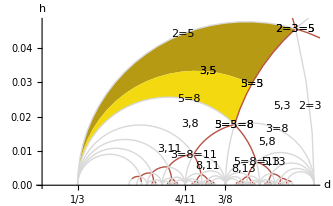

```mathematica
Txb0502VanItersonZoom =Ch4VanItersonZoom;
txbExport[Txb0502VanItersonZoom]
```

## Txb0503NonOpposed

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];

Ch4NonOpposed := Module[{tieColour,lattice},
lattice = latticeCreateDH[latticeDHNonOpposedTC[{2,5}], {-0.1,0.5}];
tieColour[1]=jParastichyColour[1];tieColour[2]=jParastichyColour[3];tieColour[3]=jParastichyColour[3];
ch4showParastichyLines[lattice,tieColour]
];
```

```mathematica
ch4showParastichyLines[lattice_,lineColourFunction_:jParastichyColour]  :=  Module[{ll,llines,paraset,plines},
ll = latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{FaceForm[White],latticeCircles[lattice]/. Circle->Disk},
, {Thick,MapIndexed[{lineColourFunction[First[#2]],#1}&,llines]}
,{PointSize[Small],Point[latticePoints[lattice]]}
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];

insetLattice[dh_] := Module[{lattice},
lattice = latticeCreateDH[dh,{0,2}];
Inset[ch4showParastichyLines[lattice],dh,Center,0.1]
];

Txb0503NonOpposed := Ch4NonOpposed
```

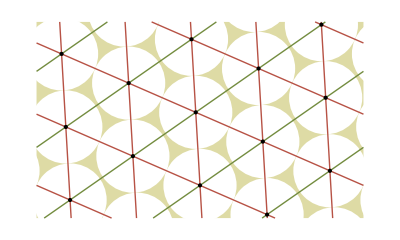

```mathematica
txbExport[Txb0503NonOpposed]
```

## Txb0504 Unfolding

```mathematica
jRotate[x_,y_] := Rotate[x,y,{0,0}];
triset1:= Module[{theta,trilen,lin,lint},
theta = 10 Degree;
trilen = 0.4;
lin = Line[{{-0.05,0},{0.05+trilen,0}}];
lint =Translate[jRotate[lin,theta], trilen*{Cos[120 Degree+theta],Sin[120 Degree+theta]}];
res = 
{
Directive[Thickness[Medium],Gray],
jRotate[lin,theta],
jRotate[lin,theta+ 60 Degree],
jRotate[lin,theta+ 120  Degree],
lint,
Rotate[lint,120 Degree,trilen*{Cos[60 Degree+theta],Sin[60 Degree+theta]}]
};
res
];


bifurcationLineColours = {viSwatch["TouchingCircle"],viSwatch["NonTouchingCircle"],viSwatch["NonOpposedTouchingCircle"]};

figUnfold:= Module [{grayColour,triset2,arrow,a3,a5,a8,theta,trilen,f1,f2,f3,h358,prunedTree,aStretch,makehbox,tclabel},
theta = 10 Degree;
grayColour = Black;
triset2 = {Rotate[triset1,120 Degree,{0,0}],Rotate[triset1,240 Degree,{0,0}]};
trilen = 0.4;
arrow = Arrow[{{0,0},{trilen,0}}];
a3 = jRotate[arrow,theta];
a8 = jRotate[arrow,theta+60 Degree];
a5 = jRotate[arrow, theta+120 Degree];

(*f1 = Map[{bifurcationLineColours[[1]],viiPrimaryOpposed[#]}&,{{3,5},{5,8},{3,8}}];
f3 = {bifurcationLineColours[[3]],Map[viiPrimaryNonOpposed,{{3,8}}]};
*)
f1 = Map[{bifurcationLineColours[[1]],vanItersonTouchingCirclePrimaryOpposed[#]}&,{{3,5},{5,8},{3,8}}];
f2 = {bifurcationLineColours[[2]],Map[vanItersonTouchingCircleNonPrimary,{{3,8},{5,8},{3,5}}]};
f3 = {bifurcationLineColours[[3]],Map[vanItersonTouchingCirclePrimaryNonOpposed,{{3,8}}]};
prunedTree ={Thick,{f1,f2,f3}};

h358= {triset1,triset2,
{Thick,jParastichyColour[1],a3,a8,a5},
Style[{Text["3",trilen/2 * {Cos[theta],Sin[theta]},{-2,1}]
,Text["8",trilen/2 * {Cos[theta+60 Degree ],Sin[theta+60 Degree ]},{-2,1}]
,Text["5",trilen/2 * {Cos[theta+120 Degree ],Sin[theta+120  Degree ]},{-1,-1}]
},jFont[16]]
};
aStretch[a_,phi_,ss_] :=  jRotate[Scale[jRotate[a,-theta-phi],{ss,1},{0,0}],theta+phi];

makehbox[phi_,ss_,cols_,txt_] :=  Module[{scale,ath},scale[a_] := aStretch[a,phi,ss];
If[ss>1,ath=theta+phi,ath = 180 Degree+theta+phi];
{triset1,
{Thick,cols⟦1⟧,scale[a3],cols⟦2⟧,scale[a8],cols⟦3⟧,scale[a5]},
{grayColour,jRotate[Arrow[{{0,0},{0.2,0}}],ath ]}
,
 Text[Style[txt⟦1⟧,jFont[12]],{-.25,.42}]
,
  Text[Style[txt⟦2⟧,jFont[12]],{.4,-.3},{1,0}]
 }
];
h35vi  = makehbox[60 Degree,1.2,{jParastichyColour[1],jParastichyColour[2],jParastichyColour[1]},{"3=5,8","Opposed"} ];
h35nvi = makehbox[60 Degree,0.8,{jParastichyColour[2],jParastichyColour[1],jParastichyColour[2]},{"8,3=5","" }];
h38nvi = makehbox[120  Degree,0.8,{jParastichyColour[2],jParastichyColour[2],jParastichyColour[1]},{"5,3=8" ,"" }];
h38vi = makehbox[30  Degree,0.8,{jParastichyColour[1],jParastichyColour[1],jParastichyColour[2]},{"3=8,5","Nonopposed"}];
h58nvi = makehbox[90  Degree,1.2,{jParastichyColour[1],jParastichyColour[2],jParastichyColour[2]},{"3,5=8","" }];
h58vi = makehbox[90  Degree,0.8,{jParastichyColour[2],jParastichyColour[1],jParastichyColour[1]},{"5=8,3","Opposed"} ];
tcLabel[t_] := {Cos[(π /3)(1+t)],Sin[(π /3)(1+t)]};
rbox = {{-1/2,-.4},{1/2,1/2}};

hexbox[{m_,n_},s_,box_] := {
Inset[
Graphics[
{Arrowheads[0.1],FaceForm[White],EdgeForm[grayColour],Apply[Rectangle,rbox],box},PlotRange->1.01*Transpose[rbox]
]
,latticeMoebiusTransform[{m,n}][tcLabel[s]] ,{0,0},0.003]
};

hexboxes := Style[{
hexbox[{3,5},0,h358],
hexbox[{3,8},1.2,h38nvi],
hexbox[{3,8},0.78,h38vi],
hexbox[{3,5},0.2,h35vi],
hexbox[{3,5},-0.25,h35nvi],
hexbox[{5,8},0.75,h58vi],
hexbox[{5,8},1.2,h58nvi]
},
jFont[16]];

legend = LineLegend[
Map[Directive[Thick,#]&,bifurcationLineColours],{"Opposed touching-circle","Not touching circle","Not opposed"}
,LabelStyle-> Directive[FontFamily->jStyle["FontFamily"]]];

bifplot = 
 Graphics[
{  
prunedTree
,hexboxes
},
PlotRange->
{{0.37,0.385},{.01,0.025}}

,PlotRangeClipping->True,
AspectRatio->Automatic,Axes->False,AxesOrigin->{0.37,0.01},Ticks->False,
AxesLabel->{"d","h"},jFont[16],
ImageSize->600
, BaseStyle->  {FontFamily->  jStyle["FontFamily"]}
];

Legended[bifplot,Placed[legend,{{1,1},{1,1}}]]
];

Ch4Unfolding := figUnfold;
```

```mathematica
Ch4Unfolding
```

-Graphics-

```mathematica
Txb0504Unfolding= Ch4Unfolding;
```

```mathematica
txbExport[Txb0504Unfolding]
```

-Graphics-

## Txb0505Pruned

```mathematica
opposedTreePlot[mnPairs_,labelPairs_,highLightPairs_,opts:OptionsPattern[]] := Module[{regionLabel,prunedTree},
regionLabel[mn_] := panelLabel[mn,vanItersonLabelPoint[mn],0.15];

prunedTree = {
Map[{If[MemberQ[highLightPairs,#],Directive[{Thick,viSwatch["TouchingCircle"]}],viSwatch["TouchingCircle"]],vanItersonTouchingCirclePrimaryOpposed[#]}&,mnPairs]
,{viSwatch["NonOpposedTouchingCircle"],Map[vanItersonTouchingCirclePrimaryNonOpposed,mnPairs]}
 };



Graphics[
{
{Thin,LightGray,Map[vanItersonTouchingCircleNonPrimary,mnPairs]}
,  prunedTree
, Map[touchingCircleLabel,labelPairs]
},
Evaluate[FilterRules[{opts}, Options[Graphics]]]
]
];

Ch4Pruned := Module[{mnPairs,labelPairs,tplaces,ticks,g},
mnPairs = Nest[addSubTree,{{1,2}},6];
labelPairs =  Join[Nest[addSubTree,{{1,2}},2],{{4,5}},{}];tplaces= Append[Table[ (GoldenRatio)/(1+k GoldenRatio),{k,4,3,-1}],1/GoldenRatio^2];
ticks  = Append[ Transpose[{tplaces,tplaces /.GoldenRatio-> τ}],1/2];

g = 
opposedTreePlot[ mnPairs,labelPairs,{},PlotRange->
{{0.15,0.5},{0,0.25}}
,Axes->True,Ticks->{ticks,None}
,AxesLabel-> Map[Style[#,Italic,FontFamily->jStyle["FontFamily"]]&,{"d","h"}]
 ,BaseStyle->  {FontFamily->  jStyle["FontFamily"]}
];
Legended[g,Placed[
LineLegend[{
viSwatch["TouchingCircle"],
viSwatch["NonOpposedTouchingCircle"]},
{"Touching circle opposed"
,"Touching circle not opposed"
}
,LabelStyle->Directive[FontFamily->jStyle["FontFamily"]]]
,{{0.07,1},{0,2}}]
]
];
```

```mathematica
Txb0505Pruned=Ch4Pruned
```

-Graphics-

## Txb0506Renormalisation

```mathematica
showRenormalisation[{m_,n_},{d_,h_}] := Module[{},
baseLattice= latticeCreateDH[{d,h},{-1.2,2.2}];
rdh = latticeMoebiusTransform[{m,n}][{d,h}];
lattice = latticeCreateDH[rdh,{-4,4}];

cylinderLU = latticeGetCylinder[lattice][[2]];
cylinder := Rectangle[{-.5,cylinderLU[[1]]},{0.5,cylinderLU[[2]]}];
plotRange =  {{-0.6,1.6},{cylinderLU[[1]],cylinderLU[[2]]}};
latticepointvalues = latticeGraphicPoints[lattice];
 {pm,pn} = latticePrincipalParastichyPair[lattice];
pnDelta = latticePoint[lattice,pn];
ppts ={
jParastichyColour[3],latticeGraphicsPoint[lattice,0],
jParastichyColour[1], latticeGraphicsPoint[lattice,pm],
jParastichyColour[2],Point[pnDelta],
White,Point[latticePoint[lattice,1]],
Style[Text["1",latticePoint[lattice,1]],Directive[Black,FontFamily->jStyle["DisplayFontFamily"],FontSize->Scaled[0.02]]]
};
pLines= {
jParastichyColour[1], Line[{latticePoint[lattice,0],latticePoint[lattice,pm]}],
jParastichyColour[2],Line[{latticePoint[lattice,0],latticePoint[lattice,pn]}]
};
ptPrimary=latticePoint[lattice,3];
ptOrigin = latticePoint[lattice,0];
angle=ArcTan@@ptPrimary;
rotation=  RotationTransform[-angle,ptOrigin];
stretch = 1/Norm[ptPrimary-ptOrigin];
normalisation = ScalingTransform[{stretch,stretch},ptOrigin]@*rotation;
tHeight=2;
g1List={
{ jStyle["CylinderColour"],cylinder}
,{Black,PointSize[Small],Table[Translate[latticepointvalues,{nc,0}],{nc,-3,3}]}
,pLines
,{{PointSize[Medium],ppts}}
,{FaceForm[White],EdgeForm[Black]}
, {Thick,jParastichyColour[1]}
};
{redx,redy}=normalisation[latticePoint[lattice,3]];
{greenx,greeny}=normalisation[latticePoint[lattice,0]];
widthx=redx-greenx;
baseCylinder= {Opacity[0.5],Gray,Rectangle[{greenx-widthx/2,-tHeight},{redx-widthx/2,tHeight}]};
g2=Module[{},
Graphics[
{
GeometricTransformation[g1List,rotation],
baseCylinder},
PlotRange->tHeight*{{-1,1},{-1,1}}
]
];
g3=Module[{},
Graphics[
{
GeometricTransformation[g1List,normalisation],
baseCylinder
},
PlotRange->tHeight*{{-1,1},{-1,1}}
]
];
arrowSize=Small;
mid=angle/5;
comid = 90 Degree - mid;


rotor =Graphics[{
Gray,Circle[{0,0},1,{0 ,angle}]
,jParastichyColour[1],
,Dotted,Line[{{0,0},{Cos[angle],Sin[angle]}}]
,Arrowheads[.15]
(*,Arrow[RotationTransform[90 Degree,{Cos[mid],Sin[mid]}][Line[{1.01*{Cos[mid],Sin[mid]},{Cos[mid],Sin[mid]}}]]],
*),Line[{{0,0},{1,0}}],
,PointSize[Medium],Point[{{Cos[angle],Sin[angle]},{1,0}}]
}
,PlotRange->-2*{{-1,1},{-1,1}},AspectRatio->1];
scalar = Graphics[{
Gray,
Arrowheads[{{arrowSize,1}}],
Arrow[Line[{{0,0},{1,0}}]],
Arrow[Line[{{0,0},{-1,0}}]],
Arrow[Line[{{0,0},{0,-1}}]],
Arrow[Line[{{0,0},{0,1}}]],jParastichyColour[1],
,PointSize[Medium],Point[{1/stretch,0}],Point[{1,0}]
}
,PlotRange->-2*{{-1,1},{-1,1}},AspectRatio->1];

Show[GraphicsRow[{
Graphics[g1List,PlotRange->tHeight*{{-1,1},{-1,1}}],Framed[rotor,FrameStyle->None] ,g2,
Framed[scalar,FrameStyle->None],g3},0],ImageSize->600]
];
```

```mathematica
Txb0506Renormalisation = showRenormalisation[{2,3},{17/72,1}];
txbExport[Txb0506Renormalisation]
```

-Graphics-

## Txb0507VIQ

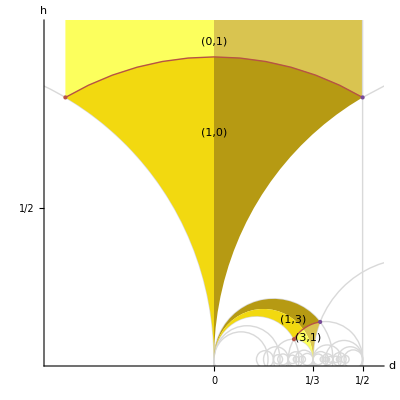

```mathematica
figVanItersonQ[mn_]:= Module[{mnPairs,g,plotRange,aspectRatio,pr2},
Off[Divide::infy];
mnPairs = Nest[addSubTree,{{0,1}},6];

g  = {  jFont[12]
,{LightGray,Map[vanItersonTouchingCircle,mnPairs] /.  ∞ -> 1.2,Translate[vanItersonTouchingCirclePrimary[{0,1}],{1,0}]
}
,colourPolygonNew[{0,1},2]
, colourPolygonNew[{1,0}]
,colourPolygonNew[mn]
,colourPolygonNew[Reverse@mn]
, {
{ viSwatch["TouchingCircle"]
,vanItersonTouchingCirclePrimary[{0,1}],
vanItersonTouchingCirclePrimary[mn]}
}
,{PointSize[Large]
,jParastichyColour[1],
Point[vanItersonRegionPoints[{0,1}]["LeftTriplePoint"]]
,Point[vanItersonRegionPoints[mn]["LeftTriplePoint"]]
,jParastichyColour[2],
,Point[latticeMoebiusTransform[mn][{ -1/2 , Sqrt[3]/2}]]
,Point[{ 1/2 , Sqrt[3]/2}]
}
};
plotRange = {{-0.55,0.55},{0,1.1}} ;
aspectRatio = (plotRange⟦2,2⟧-plotRange⟦2,1⟧)/(plotRange⟦1,2⟧-plotRange⟦1,1⟧);
pr2 = {-0.05,0.4};
Off[Divide::infy];
bg=Directive[Opacity[0.5],White];

{Graphics[{g, {
 {Text["(0,1)",{0,1.05},Background->bg]},
, {Text["(1,0)",{0,0.75},Background->bg]},
{{Text[StringTemplate["(``,``)"][mn[[1]],mn[[2]]],vanItersonLabelPoint[mn],Background->bg]},
{Text[StringTemplate["(``,``)"][mn[[2]],mn[[1]]],vanItersonLabelPoint[Reverse[mn]],Background->bg]}
}
}}
,PlotRange->plotRange,PlotRangeClipping->True
,Axes->{True,True}
,Ticks ->{{{0,0},{1/3,1/3},{1/2,1/2}},{1/2}}
,AxesLabel-> Map[Style[#,Italic,FontFamily->jStyle["FontFamily"]]&,{"d","h"}]
, BaseStyle->  {FontFamily->  jStyle["FontFamily"]}
]
}
]
Ch4VIQ := GraphicsGrid[{figVanItersonQ[{1,3}]}]
Ch4VIQ
```

```mathematica
Txb0507VIQ:=Ch4VIQ;
txbExport[Txb0507VIQ]
```

-Graphics-

## Txb0508SpiralPacking

```mathematica
countbins = AssociationThread[{"Below","Average","Above"},Partition[{0,8,12,100},2,1]];
countToBin [count_] := First@Keys@Select[Map[ IntervalMemberQ[Interval[#],count]&,countbins],TrueQ];
colourBin = AssociationThread[{"Below","Average","Above"},{jParastichyColour[4],jStyle["CylinderColour"],
jParastichyColour[1]}];

colourFunction[count_] :=colourBin[countToBin[count]];
```

```mathematica
angleDistributionPlot[angle_] := Module[{},
angleBins = Subdivide[0,2π,100];
angleHalfWidth = π/100;
cmax = 20;
bincounts = BinCounts[angleDistribution[angle],{angleBins}];
angleCount  = Transpose[ {Drop[angleBins  ,-1],bincounts}];
colourFunction[count_] :=colourBin[countToBin[count]];

Graphics[
Map[{colourFunction[#⟦2⟧], Annulus[ {0,0},1,{#⟦1⟧-angleHalfWidth,#⟦1⟧+angleHalfWidth}]}&,angleCount]
]
];

makeCh4SpiralPacking := Module[{},
nPoints = 1000;
rise = 1/nPoints;
spiral[angle_] := Table[ n rise * {Cos[ n angle],Sin[n angle]},{n,nPoints}];
angleDistribution[angle_] :=  Table[ Mod[ n angle,2π],{n,nPoints}];
angles =   GoldenAngle *{ 1/1.001,1,1.001};
alabels =alabels =Map[ Graphics[{EdgeForm[None],FaceForm[None],Rectangle[{-1/2,-.1},{1/2,0.1}],Text[Style[#,setGill],{0,0}]}]&, {"τ^-2/1.001","τ^-2","1.001 τ^-2"}];
boxes = GraphicsColumn/@ (Transpose@{
alabels,
Map[Graphics[Point[spiral[#]]]&,angles],
Map[angleDistributionPlot,angles]
});
g= GraphicsRow[Append[boxes,Graphics[]]];
legbox := SwatchLegend[ Values[colourBin],Keys[colourBin],LabelStyle->setGill,
LegendLabel->"Angular node density"];

Legended[g,Placed[legbox,{{.95,0.2},{1,0}}]]
];

Txb0508SpiralPacking:= makeCh4SpiralPacking
```

```mathematica
txbExport[Txb0508SpiralPacking]
```

-Graphics-

## Txb0509PackingTreePlot

```mathematica
makePackingPlot := Module[{},
 swatch= {Transparent,jParastichyColour[4],jStyle["CylinderColour"],jParastichyColour[1]};

(* contour plot bug puts lines in texture colours ...*) 
pr={{0.25,0.45},{0.005,0.2}};

globalContourPlotImage = ContourPlot[
packingOf[{d,h}],{d,0.25,0.45},{h,0.005,0.2}
, Contours-> {0.5,0.7,0.8},Axes->False,Frame->False
,ContourStyle->None
,ContourShading->swatch,
,PlotRange->pr
,PlotRangePadding->0,
MaxRecursion->2
];
img=Rasterize[globalContourPlotImage];
globalContourPlotLines = ContourPlot[
packingOf[{d,h}],{d,0.25,0.45},{h,0.005,0.2}
, Contours-> {0.5,0.7,0.8},Axes->False,Frame->False
,ContourShading->None
,PlotRange->pr
,PlotRangePadding->0,MaxRecursion->2
];
rectangle=Rectangle@@Transpose[pr];


mnPairs= Join [{ {0,1},{1,1}},pairsTodo[.005,50]];
globalContourPlot = Show[
Graphics[{Texture[img],rectangle}
,FrameTicks->{{ {0.005,0.1,0.2},None},{{0.25,{GoldenAngle/(2π),"τ"},0.45},None}}
,Frame->{{True,False},{True,False}}
,PlotRangeClipping->True
,BaseStyle->Directive[jFont[12]],FrameStyle->Directive[Italic,FontFamily->jStyle["FontFamily"]]
,FrameLabel->{"d","h"}
,PlotRange->pr
,PlotRangePadding->0
,Epilog->{{White,Line[{{GoldenAngle/(2π),0.0},{GoldenAngle/(2π),0.9}}]}}
]
,Graphics[{Gray,Map[vanItersonTouchingCirclePrimary,mnPairs]},PlotRange->pr,PlotRangeClipping->True]
,globalContourPlotLines
];

globalPackingPlot = 
Plot[packingOf[{d,0.005}],{d,0.25,.45},BaseStyle->jFont[12],AxesLabel->{"d","β"},
(*Ticks->{ {0.25,{GoldenAngle/(2π),"τ"},0.45},{0.1,π/(2√3)}},
*)FrameTicks->{{ 0.1,{π/(2√3),π/(2√3)}},{{0.25,{GoldenAngle/(2π),"τ"},0.45},None}}
,FrameLabel->{"h","β"}
,FrameStyle->Directive[Italic,FontFamily->jStyle["FontFamily"]]
,Frame->{{True,False},{True,False}}
,PlotRange->{{0.25,0.45},{0,1}}
,PlotStyle->{jParastichyColour[1]}
,AspectRatio->1
,GridLines->{ {GoldenAngle/(2π)},{π/(2√3)}}
,PlotRangePadding->prp
,Epilog->{{LightGray,Line[{{GoldenAngle/(2π),0.09},{GoldenAngle/(2π),0.9}}]}}
];

;

packingOf[{d_,h_}] := Module[{lattice,pm},
lattice=latticeCreateDH[{d,h}];
pm=lattice["parastichyVectors"][[1]];
beta = π  pm .pm / (4 h);
beta
];

contourLegend = 
Framed[
SwatchLegend[Reverse@swatch,
{"Close to hexagonal","Tight","Loose","Loosest"}
,LabelStyle->Directive[jFont[12]]
],Background->White];
leg = Placed[contourLegend,{{0.05,0.95},{0,1}}];
];
```

```mathematica
makePackingPlot;
```

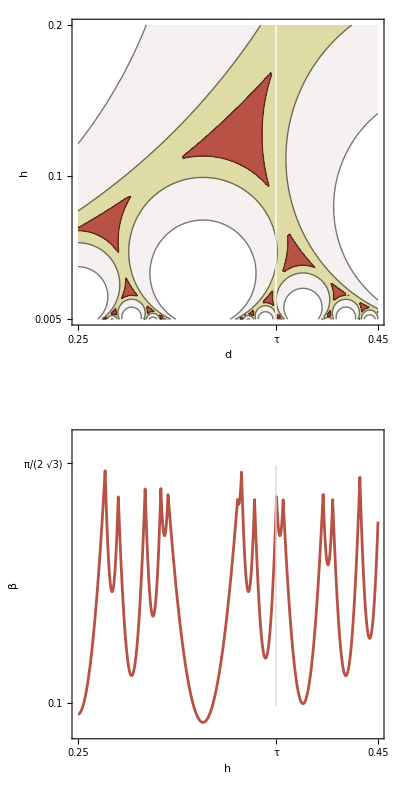

```mathematica
Txb0509PackingTreePlot = Legended[GraphicsColumn[{globalContourPlot,globalPackingPlot},Alignment->Bottom],
{Placed[contourLegend,{0.4,1.55}],Placed[LineLegend[{jParastichyColour[1]},{"Packing β at h=0.005"},LabelStyle->Directive[FontFamily->jStyle["FontFamily"]]
],{0.4,.9}]}]
```

## Txb0510JugacyRevisited

```mathematica
makeJugacyPlot := Module[{},
mnPairs= Join [{ {0,1},{1,1}},pairsTodo[.005,50]];
pr={{0,0.5},{0,0.3}};
family=Map[vanItersonTouchingCirclePrimary,mnPairs];
scaledFamily[n_] := GeometricTransformation[family,ScalingTransform[{1/n,1/n}]];
pairedFamily[n_] := {scaledFamily[n],GeometricTransformation[scaledFamily[n],ReflectionTransform[{1,0},{1/(2n),0}]]};
friezeFamily[n_] := Table[GeometricTransformation[pairedFamily[n],TranslationTransform[{ j/n,0}]],{j,-2,2}];
jfamily[n_] := {swatch[n],friezeFamily[n]};
Legended[Graphics[Table[jfamily[n],{n,1,4}],Axes->True,PlotRange->{{0,1/2},{0,0.3}},
Ticks->{{0,1/2},{0,0.3}},AxesLabel->{"d","h"},LabelStyle->Directive[FontFamily->jStyle["FontFamily"]]]
,LineLegend[Table[swatch[nc],{nc,1,4}],Table[StringTemplate["Jugacy ``"][nc],{nc,1,4}],LabelStyle->Directive[FontFamily->jStyle["FontFamily"]]]]
];
Txb0510MultiJugacy:=makeJugacyPlot;
```

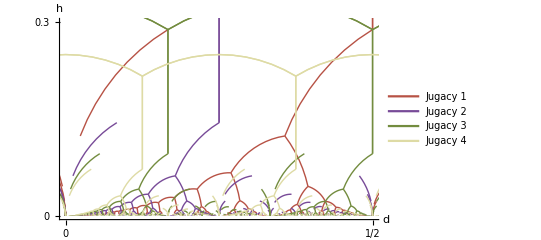

```mathematica
txbExport@Txb0510MultiJugacy
```